# Лабораторная работа №1 Математические модели динамики численности популяции одного вида

КМ2016, 3 курс, 6 семестр
Гаврис Максим
18 февраля-2019

## Задание 1. Модель Мальтуса

### 1.

```mathematica
DSolve[{Ν'[t]==(α[t]-β[t]) Ν[t],Ν[t0]==N0},Ν[t],t]//First
```

{Ν[t]→ⅇ^(-∫_1^t0 α[K[1]]ⅆK[1]+∫_1^t (α[K[1]]-β[K[1]])ⅆK[1]-∫_1^t0 -β[K[1]]ⅆK[1]) N0}

### 2.

```mathematica
MaltusSolution[t_,t0_,N0_,α0_,β0_]:=DSolve[{Ν'[t]==(α0-β0) Ν[t],Ν[t0]==N0},Ν[t],t]⟦1,1,2⟧
```

```mathematica
{t0,N0}={0,10000};
t0=0;
N0=10000;
```

```mathematica
MaltusSolution[t,t0,N0,α0,β0]
```

10000 ⅇ^(t (α0-β0))

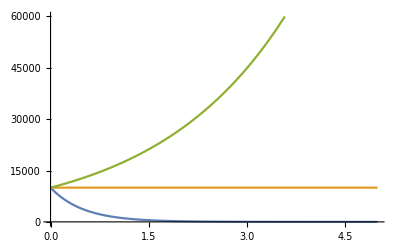

```mathematica
Plot[Evaluate[MaltusSolution[t,t0,N0,α0,β0]/.{α0->#⟦1⟧,β0->#⟦2⟧}&/@{{3,5},{3,3},{1.5,1}}],{t,0,5},PlotRange->{{0,5},{-5,60000}}]
```

### 3.

#### При t→∞ и α_0 < β_0 для модели Мальтуса имеем экспоненциальное убывание. Колебания отсутствуют При t→∞ и α_0 > β_0 для модели Мальтуса имеем экспоненциальное возрастание. Колебания отсутствуют При α_0 = β_0 значения графика не изменяются (он параллелен оси t).Константа

### 4.

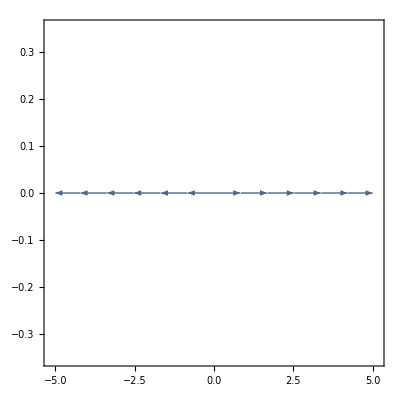

```mathematica
StreamPlot[{x,0},{x,-5,5},{y,-0.2,0.2}]
```

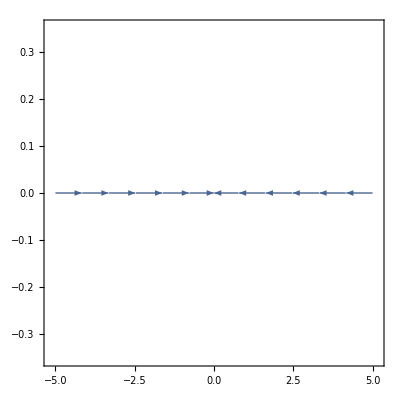

```mathematica
StreamPlot[{-x,0},{x,-5,5},{y,-0.2,0.2}]
```

## Задание 2. Логистическая модель (модель Ферхюльста)

### 1.

```mathematica
DSolve[{Ν'[t]==Ν[t] k (1-Ν[t]/Np),Ν[t0]==N0},Ν[t],t]//First
```

{Ν[t]→(10000 ⅇ^(k t) Np)/(-10000+10000 ⅇ^(k t)+Np)}

### 2.

```mathematica
LogModelSolution[t_,t0_,k_,N0_]:=DSolve[{Ν'[t]==Ν[t] k (1-Ν[t]/Np),Ν[t0]==N0},Ν[t],t]⟦1,1,2⟧
```

```mathematica
{k,t0,Np}={2,0,1000000};
```

```mathematica
ClearAll[N0]
```

```mathematica
LogModelSolution[t,t0,k,N0]
```

(1000000 ⅇ^(2 t) N0)/(1000000-N0+ⅇ^(2 t) N0)

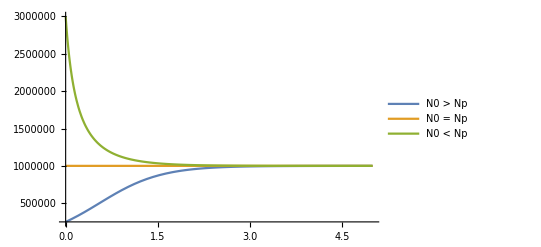

```mathematica
Plot[Evaluate[LogModelSolution[t,t0,k,N0]/.{N0->Np #}&/@{0.25,1,3}],{t,0,5},PlotRange->Full,PlotLegends->{"N0 > Np","N0 = Np", "N0 < Np"}]
```

### 3.

#### При t→∞ и N_0 < N_p для логистической модели имеем экспоненциальное убывание. Колебания отсутствуют При t→∞ и N_0 > N_p для логистической модели имеем ??? возрастание.Колебания отсутствуют При N_0 = N_p значения графика не изменяются (он параллелен оси t).Константа

### 4.

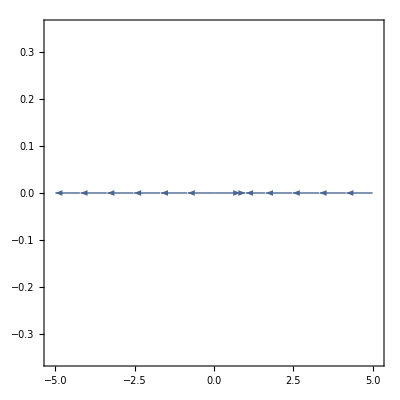

```mathematica
StreamPlot[{x (1-x),0},{x,-5,5},{y,-0.2,0.2}]
```

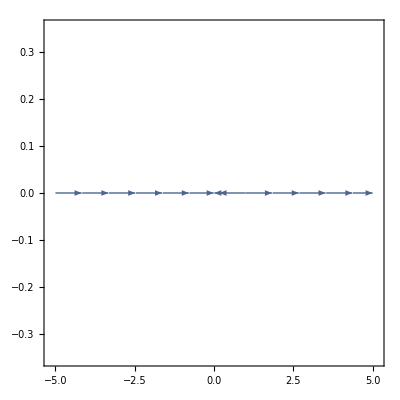

```mathematica
StreamPlot[{-x (1-x),0},{x,-5,5},{y,-0.2,0.2}]
```

## Задание 3. Нелинейный аналог модели Мальтуса

### 1.

```mathematica
ClearAll[t0,N0,α0,β0]
```

```mathematica
DSolve[{Ν'[t]==Ν[t] (α0 Ν[t]-β0),Ν[t0]==N0},Ν[t],t]//First
```

{Ν[t]→(ⅇ^(t0 β0) N0 β0)/(-ⅇ^(t β0) N0 α0+ⅇ^(t0 β0) N0 α0+ⅇ^(t β0) β0)}

### 2.

```mathematica
MaltusNonleanSolution[t_,t0_,N0_,α0_,β0_]=DSolve[{Ν'[t]==Ν[t] (α0 Ν[t]-β0),Ν[t0]==N0},Ν[t],t]⟦1,1,2⟧
```

(ⅇ^(t0 β0) N0 β0)/(-ⅇ^(t β0) N0 α0+ⅇ^(t0 β0) N0 α0+ⅇ^(t β0) β0)

```mathematica
ClearAll[t0,N0,α0,β0]
```

```mathematica
{t0,α0,β0}={0,5,100};
```

```mathematica
Nkp=β0/α0
```

20

```mathematica
MaltusNonleanSolution[t,t0,N0,α0,β0]
```

(100 N0)/(100 ⅇ^(100 t)+5 N0-5 ⅇ^(100 t) N0)

```mathematica
ClearAll[N0]
```

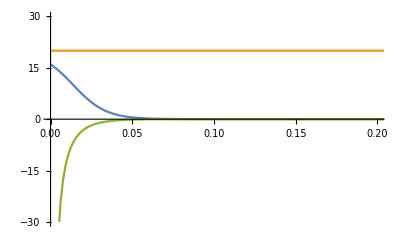

```mathematica
Plot[Evaluate[MaltusNonleanSolution[t,t0,N0,α0,β0]/.{N0->Nkp #}&/@{0.8,1,100}],{t,0,5},PlotRange->{{0,0.2},{-30,30}}]
```

### 3.

#### При t→∞ и N_0 < N_кр для логистической модели имеем экспоненциальное убывание. Колебания отсутствуют При N_0 = N_кр значения графика не изменяются (он параллелен оси t).Константа При t→∞ и N_0 > N_кр для логистической модели имеем точку разрыва. ???

### 4.

```mathematica
StreamPlot[{x (x-1),0},{x,-5,5},{y,-0.2,0.2}]
```

-Graphics-

```mathematica
StreamPlot[{-x (x-1),0},{x,-5,5},{y,-0.2,0.2}]
```

-Graphics-

## Задание 4. Предсказание на основании моделирования

```mathematica
ClearAll[t0,N0,α0,β0]
```

```mathematica
entityBelarus=Entity["Country","Belarus"];
```

```mathematica
{N0,α0,β0}=QuantityMagnitude@EntityValue[entityBelarus,#]&/@{"Population","BirthRateFraction","DeathRateFraction"}
```

{9468338,0.011874,0.013346}

```mathematica
EntityValue[entityBelarus,#,"Date"]&/@{"Population","BirthRateFraction","DeathRateFraction"}
```

{2017,2017,2017}

```mathematica
t0=2017;
```

#### График функции для всех значений свойства “Population”, которые хранятся в базе знаний

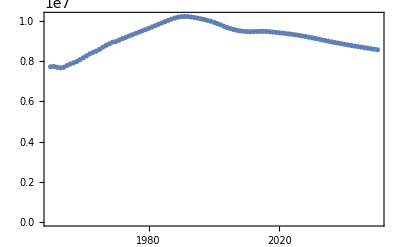

```mathematica
DateListPlot[Dated[entityBelarus,All]["Population"], PlotRange->{{"1950","2050"},All},Joined->False]
```

#### Предсказания для модели Мальтуса

```mathematica
MaltusSolution[t,t0,N0,α0,β0]
```

1.84376×10^8 ⅇ^(-0.001472 t)

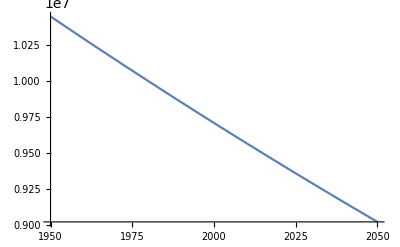

```mathematica
P1 =Plot[MaltusSolution[t,t0,N0,α0,β0]/.(t->τ),{τ,1950,2050},PlotRange->{{1950,2050},All}]
```

#### Предсказания для нелинейного аналога модели Мальтуса

```mathematica
MaltusNonleanSolution[t0,t0,N0,α0,β0]
```

9.46834×10^6

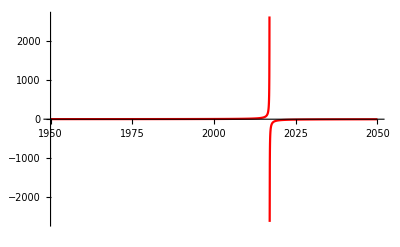

```mathematica
P2=Plot[MaltusNonleanSolution[t,t0,N0,α0,β0],{t,1950,2050},PlotRange->{{1950,2050},All},PlotStyle->Red]
```

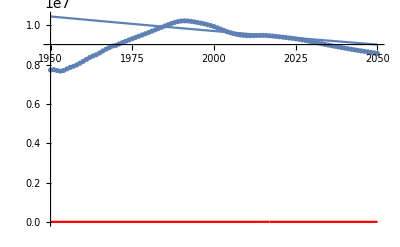

```mathematica
Show[P1,P2,ListPlot[Thread[{Range[1950,2050],QuantityMagnitude/@Dated[entityBelarus,All]["Population"]["Values"]⟦3;;⟧}],PlotRange->{1950,2050}]]
```

## Задание 5. Определение параметров модели по реальным данным

```mathematica
ClearAll[t0,N0,α0,β0]
```

```mathematica
{N0,α0,β0}=QuantityMagnitude@EntityValue[entityBelarus,#]&/@{"Population","BirthRateFraction","DeathRateFraction"}
```

{9468338,0.011874,0.013346}

```mathematica
t0=1950;
```

```mathematica
Data={#,QuantityMagnitude@Dated[entityBelarus,#]["Population"]}&/@Range[1950,2010]
```

{{1950,7722155},{1951,7742159},{1952,7698249},{1953,7666821},{1954,7698751},{1955,7780565},{1956,7856790},{1957,7912626},{1958,7982625},{1959,8075290},{1960,8167918},{1961,8262998},{1962,8365073},{1963,8438881},{1964,8501607},{1965,8590786},{1966,8694009},{1967,8786887},{1968,8864776},{1969,8946091},{1970,8977639},{1971,9051218},{1972,9120964},{1973,9187675},{1974,9252678},{1975,9316955},{1976,9380452},{1977,9443001},{1978,9505452},{1979,9568883},{1980,9633888},{1981,9700245},{1982,9767260},{1983,9834424},{1984,9901045},{1985,9966154},{1986,10030068},{1987,10091633},{1988,10146632},{1989,10189615},{1990,10216846},{1991,10226493},{1992,10219918},{1993,10200510},{1994,10173355},{1995,10142308},{1996,10109072},{1997,10073061},{1998,10033061},{1999,9986933},{2000,9933609},{2001,9872961},{2002,9807132},{2003,9740054},{2004,9676902},{2005,9621543},{2006,9575043},{2007,9536864},{2008,9507331},{2009,9486239},{2010,9473071}}

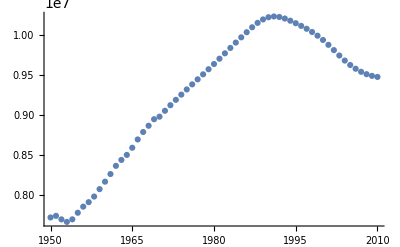

```mathematica
ListPlot[Data]
```

```mathematica
{t0,N0}=First@Data
```

{1950,7722155}

```mathematica
ClearAll[k,t]
```

```mathematica
MaltusSol=N0 Exp[k (t-t0)];
```

```mathematica
FindFit[Data,MaltusSol,{k},t]
```

{k→0.00537181}

```mathematica
MaltusSol=MaltusSol/.FindFit[Data,MaltusSol,{k},t]
```

7722155 ⅇ^(0.00537181 (-1950+t))

#### График популяционной динамики на основании модели Мальтуса

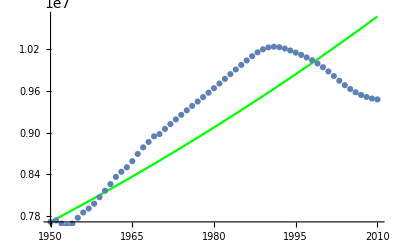

```mathematica
Show[Plot[MaltusSol,{t,1950,2010},PlotStyle->Green],ListPlot[Data]]
```

#### График относительной ошибки

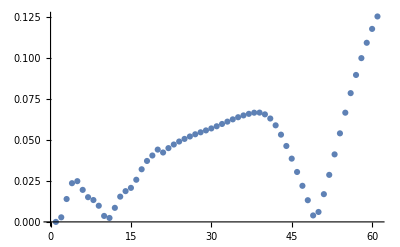

```mathematica
MathusError=Abs[Last@#-(MaltusSol/.t->First@#)]/Last@#&/@Data;
ListPlot[%]
```